```mathematica
magicGraham(primeList_):=∑_p^primeList (log((p+1)/(2 p)))/(log(p))+1
```

```mathematica
Examine3[list_] := Module[{result, current, previous, pos},
result = 0;
previous = -100;
Monitor [
For[pos=1, pos ≤ Length[list], pos++,
current = list[[pos]];
If [current == previous+1,
result +=1
];
previous = current;
];
,
pos
];
Return  [result];
]
```

```mathematica
magicGraham[Subsets[Prime[Range[1,25]],{4}]]
```

```mathematica
t_°
```

```mathematica
SuccessiveTuple[start_, length_] := Prime[Range[start, start+length-1]]
```

```mathematica
SuccessiveTuple[2,3]
```

{3,5,7}

```mathematica
myList3 = Monitor[
Table[
With[{table=GoodForTuple[tuple]},
{tuple,N[Examine3[table]],Length[table]}
],
{tuple,Table[SuccessiveTuple[l,4],{l,2,25}]}
],
tuple
]
```

{{{3,5,7,11},1.,3},{{5,7,11,13},5.,8},{{7,11,13,17},66.,140},{{11,13,17,19},4.40884×10^6,7714728},{{13,17,19,23},105446.,167928},{{17,19,23,29},332969.,486833},{{19,23,29,31},68505.,95219},{{23,29,31,37},2.02874×10^6,2669636},{{29,31,37,41},1.50892×10^6,1911248},{{31,37,41,43},1.49469×10^6,1851325},{{37,41,43,47},3.09767×10^6,3753801},{{41,43,47,53},6.18322×10^6,7369494},{{43,47,53,59},4023.,4701},{{47,53,59,61},13482.,15652},{{53,59,61,67},12326.,14051},{{59,61,67,71},31381.,35535},{{61,67,71,73},13864.,15635},{{67,71,73,79},21487.,23914},{{71,73,79,83},25725.,28583},{{73,79,83,89},17497.,19336},{{79,83,89,97},41111.,45085},{{83,89,97,101},23370.,25509},{{89,97,101,103},175527.,191073},{{97,101,103,107},81647.,88117}}

```mathematica
myList2 = Monitor[
Table[
With[{table=GoodForTuple[tuple]},
{tuple,N[Examine3[table]],Length[table]}
],
{tuple,Subsets[Prime[Range[2,25]],{3,8}]}
],
tuple
]
```

{{{3,5,7},2.1008×10^6,8403440},{{3,5,11},0.,0},{{3,5,13},0.,0},{{3,5,17},0.,0},{{3,5,19},0.,0},{{3,5,23},0.,0},{{3,5,29},0.,0},{{3,5,31},0.,0},{{3,5,37},0.,0},{{3,5,41},0.,0},{{3,5,43},0.,0},{{3,5,47},0.,0},{{3,5,53},0.,0},{{3,5,59},0.,0},{{3,5,61},0.,0},{{3,5,67},0.,0},{{3,5,71},0.,0},{{3,5,73},0.,0},«1271289»,{{53,59,71,73,79,83,89,97},0.,0},{{53,61,67,71,73,79,83,89},0.,0},{{53,61,67,71,73,79,83,97},0.,0},{{53,61,67,71,73,79,89,97},0.,0},{{53,61,67,71,73,83,89,97},0.,0},{{53,61,67,71,79,83,89,97},0.,0},{{53,61,67,73,79,83,89,97},0.,0},{{53,61,71,73,79,83,89,97},0.,0},{{53,67,71,73,79,83,89,97},0.,0},{{59,61,67,71,73,79,83,89},29.,30},{{59,61,67,71,73,79,83,97},0.,0},{{59,61,67,71,73,79,89,97},0.,0},{{59,61,67,71,73,83,89,97},0.,0},{{59,61,67,71,79,83,89,97},0.,0},{{59,61,67,73,79,83,89,97},0.,0},{{59,61,71,73,79,83,89,97},0.,0},{{59,67,71,73,79,83,89,97},0.,0},{{61,67,71,73,79,83,89,97},37.,41}}

```mathematica
myList2 = Monitor[
Table[
With[{table=GoodForTuple[tuple]},
{tuple,N[Examine3[table]],Length[table]}
],
{tuple,SuccessiveTuple[Prime[Range[2,25]],{3,8}]}
],
tuple
]
```

```mathematica
Length[myList2]
```

1271325

```mathematica
Last[Accumulate[Map[#[[3]]&,myList2]]]
```

735185984

```mathematica
myList=Select[myList3, #[[3]]> 3&]
```

{{{3,5},3119.,9281},{{3,5,7},2.1008×10^6,8403440}}

```mathematica
Length[myList]
```

10707

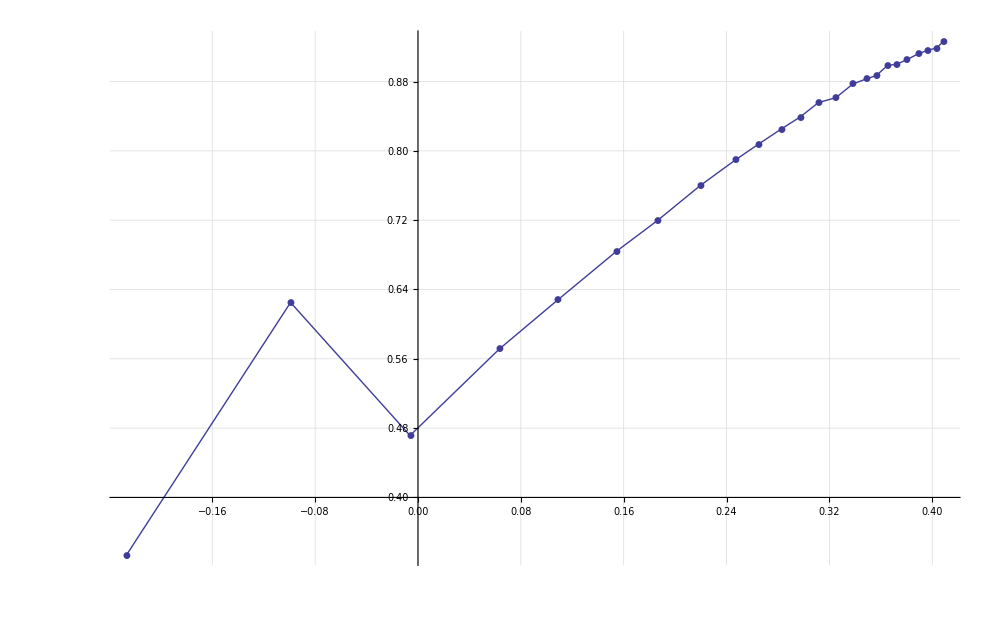

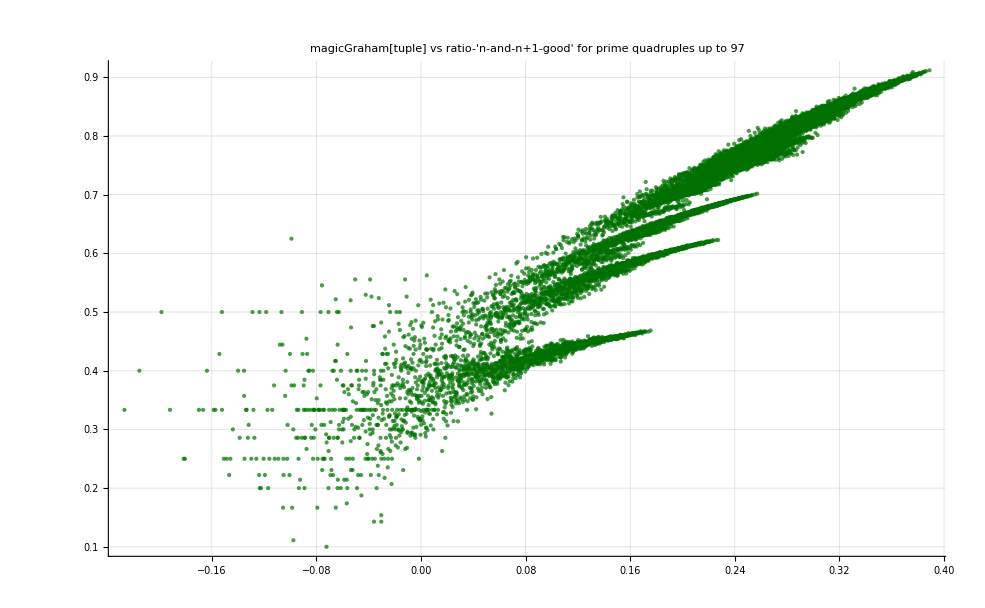

```mathematica
ListPlot[Sort[Map[{N[magicGraham[#[[1]]] ],#[[2]]/#[[3]]}&, myList3]], 
GridLines->Automatic,
GridLinesStyle->Red,
PlotMarkers->Automatic,
AxesStyle->Directive[{Thick,Darker[Black]}],
LabelStyle->{FontFamily->"Calibri", FontSize->Larger},
PlotRange->All,
Joined->True,
ImageSize->1000
]
```